```mathematica
A1=1/Sqrt[2];
A2=Sqrt[1-A1^2]
{Abs[A1]^2,Abs[A2]^2,Abs[A1]^2+Abs[A2]^2}
A1*A2
```

1/(√2)

{1/2,1/2,1}

1/2

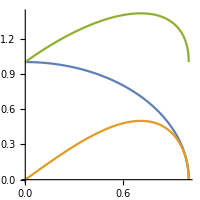

```mathematica
Plot[{Sqrt[1-a^2],a*Sqrt[1-a^2],a+Sqrt[1-a^2]},{a,0,1},AspectRatio->1]
```

```mathematica
Manipulate[Plot[{Abs[2/3(a+Exp[I k]Sqrt[1-a^2])]^2,Abs[1/3(-a+2Exp[I k]Sqrt[1-a^2])]^2,Abs[1/3(2a-Exp[I k]Sqrt[1-a^2])]^2},{k,0,2Pi},PlotRange->{0,1}],{a,0,1}]
```

```mathematica
Manipulate[Plot[{Abs[2/3(a+Sqrt[1-a^2])]^2,Abs[1/3(-a+2Sqrt[1-a^2])]^2,Abs[1/3(2a-Sqrt[1-a^2])]^2},{k,0,2Pi},PlotRange->{0,1}],{a,0,1}]
```

```mathematica
Abs[2/3(a+Sqrt[1-a^2])]^2/.a->0
```

4/9